```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]

fs=Style[#,FontSize->14]&;


<<MaTeX`

SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]

texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

\\wsl$\Ubuntu\home\pjoot\project\figures\phy452-basicstatmech

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

## Huang, problem 9.3. Relativistic gas.

### Problem a.

```mathematica
Clear[i]
$Assumptions = m > 0 && e > 0 ;i[x_, m_, e_] = Integrate[x Sqrt[x^2 - m^2], {x, m, e}]
i2[x_, m_, e_] = Integrate[x Sqrt[x^2], {x, 0, e}]
Integrate[x Sqrt[x^2 - m^2], x]
```

ConditionalExpression[1/3 ((e-m) (e+m))^(3/2), e>m]

e^3/3

1/3 (-m^2+x^2)^(3/2)

### Problem e.

```mathematica
Clear[ef, d]
ef[c_, h_, rho_, m_] = Sqrt[(3 (c h)^3 rho/(2 Pi)) + (m c^2)^2]
d = ef[3 10^8, 6.62606957 10^(-34), 1/(0.01)^3, 0]
d 6.24150934 10^(18)
```

√(c^4 m^2+(3 c^3 h^3 rho)/(2 π))

6.12402×10^-35

3.82231×10^-16

### Problem b. volume element change of vars

```mathematica
Clear[p, px, py, pz, v, npSq, j, jm]
$Assumptions = 0 ;
p = {px, py, pz}
npSq = px^2 + py^2 + pz^2 ;
(*Norm[p]^2*)
v = p/Sqrt[ m^2 + npSq/c^2]
jm = D[v, {p}] ;
jm // TraditionalForm
j = Det[ jm] ;
j // TraditionalForm
j// FullSimplify
```

$Assumptions::bass: 0 is not a well-formed assumption.

{px,py,pz}

{px/(√(m^2+(px^2+py^2+pz^2)/c^2)),py/(√(m^2+(px^2+py^2+pz^2)/c^2)),pz/(√(m^2+(px^2+py^2+pz^2)/c^2))}

(1/(√((px^2+py^2+pz^2)/c^2+m^2))-px^2/(c^2 ((px^2+py^2+pz^2)/c^2+m^2)^(3/2)) | -(px py)/(c^2 ((px^2+py^2+pz^2)/c^2+m^2)^(3/2)) | -(px pz)/(c^2 ((px^2+py^2+pz^2)/c^2+m^2)^(3/2))
-(px py)/(c^2 ((px^2+py^2+pz^2)/c^2+m^2)^(3/2)) | 1/(√((px^2+py^2+pz^2)/c^2+m^2))-py^2/(c^2 ((px^2+py^2+pz^2)/c^2+m^2)^(3/2)) | -(py pz)/(c^2 ((px^2+py^2+pz^2)/c^2+m^2)^(3/2))
-(px pz)/(c^2 ((px^2+py^2+pz^2)/c^2+m^2)^(3/2)) | -(py pz)/(c^2 ((px^2+py^2+pz^2)/c^2+m^2)^(3/2)) | 1/(√((px^2+py^2+pz^2)/c^2+m^2))-pz^2/(c^2 ((px^2+py^2+pz^2)/c^2+m^2)^(3/2)))

-px^2/(c^2 ((px^2+py^2+pz^2)/c^2+m^2)^(5/2))+1/(((px^2+py^2+pz^2)/c^2+m^2)^(3/2))-py^2/(c^2 ((px^2+py^2+pz^2)/c^2+m^2)^(5/2))-pz^2/(c^2 ((px^2+py^2+pz^2)/c^2+m^2)^(5/2))

(c^6 m^2 √((c^2 m^2+px^2+py^2+pz^2)/c^2))/((c^2 m^2+px^2+py^2+pz^2)^3)

### problem b. attempt the integrals

```mathematica
i[x_, beta_, mu_, e0_] = (x^2 - 1)^(3/2)/(x^5 (E^(beta e0 x - beta mu) + 1)) ;
i2[x_, beta_, mu_, e0_] = (x^2 - 1)^(1/2)/(x^4 (E^(beta e0 x - beta mu) + 1)) ;
i[x, β, μ, Subscript[e, 0]] // TraditionalForm
i2[x, β, μ, Subscript[e, 0]] // TraditionalForm
$Assumptions = β > 0 && μ < 1 &&  Subscript[e, 0] > 0 ;
Integrate[ i[x, β, μ, Subscript[e, 0]], {x, 1, Infinity}]
Integrate[ i2[x, β, μ, Subscript[e, 0]], {x, 1, Infinity}]
```

((x^2-1)^(3/2))/(x^5 (ⅇ^(β e_0 x-β μ)+1))

(√(x^2-1))/(x^4 (ⅇ^(β e_0 x-β μ)+1))

∫_1^∞ ((-1+x^2)^(3/2))/((1+ⅇ^(-β μ+x β e_0)) x^5)ⅆx

∫_1^∞ (√(-1+x^2))/((1+ⅇ^(-β μ+x β e_0)) x^4)ⅆx

### Problem b. second round of the integrals.

```mathematica
Clear[f1, f2]
f1[a_, b_, y_] = ((y+1)^2 -1)^(3/2)/(a E^(b y) + 1) ;
f2[a_, b_, y_] = (y + 1)((y+1)^2 -1)^(1/2)/(a E^(b y) + 1) ;
f1[E^(β Subscript[ϵ, 0])/z, β Subscript[ϵ, 0], y] // TraditionalForm
f2[E^(β Subscript[ϵ, 0])/z, β Subscript[ϵ, 0], y] // TraditionalForm
$Assumptions  = β > 0 && Log[z] < β && Subscript[ϵ, 0] > 0 ;
Integrate[f1[E^(β Subscript[ϵ, 0])/z, β Subscript[ϵ, 0], y], {y, 0, Infinity}] 
Integrate[f2[E^(β Subscript[ϵ, 0])/z, β Subscript[ϵ, 0], y], {y, 0, Infinity}]
```

### problem d

```mathematica
$Assumptions = efe > 1 ;
i1 = Integrate[ (x^2 - 1)^(3/2), {x, 1, efe}]
i2 = Integrate[ (x-1)x(x^2 - 1)^(1/2), {x, 1, efe}]
i1/i2 /. efe -> Sqrt[ (n/Subscript[n, 0])^(2/3) + 1] // FullSimplify
```

### problem d. attempt to sum the series in the expansion of n(zbar)

```mathematica
Clear[k, theta]
$Assumptions = k ∈ Integers && theta > 0 && k ≥ 0 ;

(* doesn't converge? *)
Sum[ (1/(k+1))^(k + s + 3/2) Gamma[ k + s + 3/2] (theta/2)^s Gamma[3/2]/(Gamma[s+1] Gamma[3/2-s])(3/2 + s)/(3/2 -s), {s, 0, Infinity}]
```

### Pressure integrals for problem d.

```mathematica
Clear[theta, s, j, k, m, t]
$Assumptions = theta > 0 && s ∈ Integers && m ∈ Integers && s ≥ 0 && m ≥ 0 ;
(*i = Integrate[ x^(m + 1/2) (1 + theta x) Sqrt[1 + theta x/2] Exp[-x(1 + s)], 
{x, 0, Infinity}]*)
j[theta_, s_] = Integrate[  ((theta x + 1)^2-1)^(3/2) Exp[-x(1 + s)], 
{x, 0, Infinity}] ;

j[ θ, s] // TraditionalForm
$Assumptions = θ > 0 && s ∈ Integers && s ≥ 0  ;
Series[j[ θ, s], {θ, 0, 5}] // FullSimplify// TraditionalForm
Clear[t]
huang93Fig2 = Plot[{BesselK[2, x], BesselK[2, 1/x]}, {x, 0.3, 3},
AxesLabel->{"z"// MaTeX} ,
PlotStyle->Thick,
BaseStyle->texStyle,
(*, PlotRange -> Full*) 
PlotLegends->Placed[{MaTeX["K_2(z)"], MaTeX["K_2(1/z)"]},{Right, Right}]
]
```

(3 θ ⅇ^((s+1)/θ) 2(s+1)/θ)/(s+1)^2

(3 √(π/2) θ^(3/2))/(s+1)^(5/2)+(45 √(π/2) θ^(5/2))/(8 (s+1)^(7/2))+(315 √(π/2) θ^(7/2))/(128 (s+1)^(9/2))-(945 √(π/2) θ^(9/2))/(1024 (s+1)^(11/2))+(31185 √(π/2) θ^(11/2))/(32768 (s+1)^(13/2))+O(θ^6)

-Graphics-

```mathematica
(3 √(π/2) θ^(3/2))/(s+1)^(5/2)+(45 √(π/2) θ^(5/2))/(8 (s+1)^(7/2))+(315 √(π/2) θ^(7/2))/(128 (s+1)^(9/2))-(945 √(π/2) θ^(9/2))/(1024 (s+1)^(11/2))+(31185 √(π/2) θ^(11/2))/(32768 (s+1)^(13/2))+O(θ^6)
```

### problem d. pressure Bessel exponential plot

(3 (-1)^s ⅇ^((1+s)/theta) theta^2 z^(1+s) BesselK[2,(1+s)/theta])/(1+s)^2

(3 θ^2 (-1)^s ⅇ^((s+1)/θ) z^(s+1) 2(s+1)/θ)/(s+1)^2

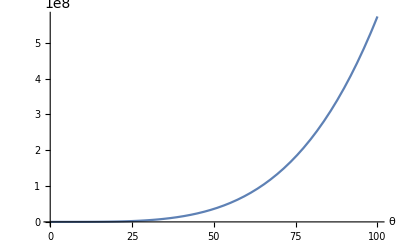

-Graphics3D-

C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit\huang93Fig3sv.svg

C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit\huang93Fig5sv.svg

```mathematica
Clear[f, theta, s, z, n, θ]
f[theta_, s_, z_] = theta(-1)^s z^(s+1)j[ theta, s] 

f[θ,s, z] // TraditionalForm
fn[theta_, n_, z_] := Sum[ f[theta, s, z], {s, 0, n}]

Manipulate[
Plot[
f[tau, s, z],
{tau, 0.1, 10},
PlotRange -> {-4, 4}
]
,{s,0,10,1}
,{{z, 0.1},0,5}
]

Manipulate[
Plot[
fn[tau, n, z],
{tau, 0.01, 3},
PlotRange -> {0, 4}
]
,{n,0,10,1}
,{{z, 0.02},0,5}
]

Clear[q]
q = Module[{w},
w = {10} ;
Plot[
Evaluate[Map[ fn[theta, #, 1] &, w]],
{theta, 0.1, 100},
AxesLabel -> { θ}
(*PlotRange -> {0, 1.5},*)
]
]
Manipulate[

Plot3D[
fn[theta, 10, z],
{theta, 0, r},
{z,0,r},
AxesLabel->{θ, z}
(*PlotRange -> {-4, 4}*)
],
{r, 5, 100}
]
Clear[r]
r = Plot3D[fn[theta,10,z],{theta,0,5},{z,0,5},AxesLabel->{θ,z}]
```

```mathematica
Clear[huang93Fig3]
huang93Fig3 = Module[{w},
w = {1, 2, 3, 4} ;
Plot[
Evaluate[Map[ f[theta, #, 1] &, w]],
{theta, 0.1, 100},
AxesLabel -> { MaTeX["\\theta"]},
PlotStyle->Thick,
BaseStyle->texStyle,
(*PlotRange -> {0, 1.5},*)
PlotLegends->Placed[Map[ MaTeX["s = " <>ToString[#]]&, w],{Right, Right}]]
]
```

-Graphics-

```mathematica
Clear[g]
$Assumptions = θ > 0 ;
g[θ_, z_] =Series[ fn[θ, 4, z], {θ, 0, 4}]/Sqrt[ Pi] // FullSimplify
g[θ, z] // TraditionalForm
```

((3 z)/(√2)-(3 z^2)/8+z^3/(3 √6)-(3 z^4)/(32 √2)+(3 z^5)/(25 √10)) θ^(5/2)+((45 z)/(8 √2)-(45 z^2)/128+(5 z^3)/(24 √6)-(45 z^4)/(1024 √2)+(9 z^5)/(200 √10)) θ^(7/2)+((315 z)/(128 √2)-(315 z^2)/4096+(35 z^3)/(1152 √6)-(315 z^4)/(65536 √2)+(63 z^5)/(16000 √10)) θ^(9/2)+O[θ]^5

θ^(5/2) ((3 z^5)/(25 √10)-(3 z^4)/(32 √2)+z^3/(3 √6)-(3 z^2)/8+(3 z)/(√2))+θ^(7/2) ((9 z^5)/(200 √10)-(45 z^4)/(1024 √2)+(5 z^3)/(24 √6)-(45 z^2)/128+(45 z)/(8 √2))+θ^(9/2) ((63 z^5)/(16000 √10)-(315 z^4)/(65536 √2)+(35 z^3)/(1152 √6)-(315 z^2)/4096+(315 z)/(128 √2))+O(θ^5)

```mathematica
Clear[h, h2]
(*h[theta_, z_] = Integrate[ ((theta x + 1)^2 - 1)^(3/2)/(z E^(-x) + 1), {x, 0, Infinity}]*)
h2[theta_, z_] = Integrate[ (1 + theta x)((theta x + 1)^2 - 1)^(1/2)/( (1/z)E^(x) + 1), {x, 0, Infinity}]
```

$Aborted

### number density calculations

```mathematica
Clear[nbinomial]
(*$Assumptions = m ∈ Integers  ;*)

nbinomial[b_, k_] = (-1)^k Binomial[-b + k, -b] (-b)/(k-b)
n[theta_, z_, n_] = Sum[ nbinomial[-2, s] (z E^(1/theta))^(s+1)/((s+1)^2) BesselK[2, (s+1)/theta], {s, 0, n}]
$Assumptions = θ > 0 ;
Clear[s]
s = Series[ n[θ, z, 2], {θ, 0, 3}]/ Sqrt[ Pi] // FullSimplify ;
s // TraditionalForm
```

-((-1)^k b Binomial[-b+k,-b])/(-b+k)

∑_(s=0)^n ((-1)^s (ⅇ^(1/theta) z)^(1+s) BesselK[2,(1+s)/theta])/(1+s)

1/36 √θ z (z (2 √6 z-9)+18 √2)+5/576 θ^(3/2) z (z (4 √6 z-27)+108 √2)+(35 θ^(5/2) z (z (8 √6 z-81)+648 √2))/55296+O(θ^(7/2))

### energy integrals

```mathematica
Clear[theta, s, u]
$Assumptions = theta > 0 && s ∈ Integers && m ∈ Integers && s ≥ 0 && m ≥ 0 ;
(*i = Integrate[ x^(m + 1/2) (1 + theta x) Sqrt[1 + theta x/2] Exp[-x(1 + s)], 
{x, 0, Infinity}]*)
u[theta_, s_] = Integrate[  x ((theta x + 1)^2-1)^(3/2) Exp[-x(1 + s)], 
{x, 0, Infinity}] ;
u[θ, s] // TraditionalForm ;
TraditionalForm[ HoldForm[ Integrate[  x ((θ x + 1)^2-1)^(3/2) Exp[-x(1 + s)] , {x , 0, Infinity}] ]== u[θ, s]]
```

∫_0^∞ x ((θ x+1)^2-1)^(3/2) exp(-x (1+s))ⅆx==(15 √π θ^3 -3/2-4(2 (s+1))/θ)/(8 (s+1)^5)

```mathematica
u[θ, s]
```

(15 √π θ^3 HypergeometricU[-3/2,-4,(2 (1+s))/θ])/(8 (1+s)^5)

```mathematica
Manipulate[
Plot[
theta^2 nbinomial[-2, s] u[theta, s], 
{theta, 0, 4},
PlotRange -> {-2000, 2000}]
,{s,0,10, 1}]
```

```mathematica
Manipulate[
Plot[theta^5 HypergeometricU[-3/2,-4,(2 (1+s))/theta],
{theta, 0, 4}(*,
PlotRange -> {-2000, 2000}*)
]
,{s,0,10, 1}]
```

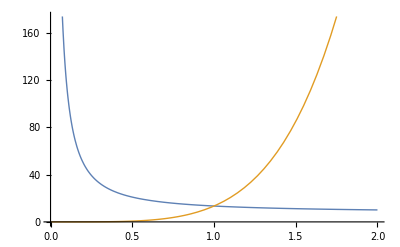

```mathematica
Clear[huang93Fig6]
huang93Fig6 = Module[{s},
s = 0;
 Plot[
{ HypergeometricU[-3/2,-4,(2 (1+s))/theta], theta^5 HypergeometricU[-3/2,-4,(2 (1+s))/theta]},
{theta, 0, 2},
PlotStyle->Thick
(*,
PlotLegends->Placed[
{TraditionalForm[ HypergeometricU[-3/2,-4,(2 (1+s))/θ]], θ^5 TraditionalForm[HypergeometricU[-3/2,-4,(2 (1+s))/θ]]},{Left, Top}]*)
]]
```

```mathematica
$Assumptions = θ > 0 ;
Series[HypergeometricU[-3/2,-4,(2 (1+s))/θ], {θ, 0, 3}] // TraditionalForm
```

(2 √2 √(s+1) s+2 √2 √(s+1))/θ^(3/2)+(21 √(s+1))/(2 √2 √θ)+(189 √θ)/(32 √2 √(s+1))-(693 θ^(3/2))/(256 (√2 (s+1)^(3/2)))+O(θ^(7/2))

```mathematica
Clear[theta, s, uu, suu]
$Assumptions = theta > 0 && s ∈ Integers && n ∈ Integers && s ≥ 0 && n ≥ 0 ;
(*i = Integrate[ x^(m + 1/2) (1 + theta x) Sqrt[1 + theta x/2] Exp[-x(1 + s)], 
{x, 0, Infinity}]*)
uu[theta_, z_,  n_] = Sum[ nbinomial[-2, s] theta^2 z^(s+1)Integrate[  ((theta x + 1)^2-1)^(3/2) Exp[-x(1 + s)](x-1 - z E^(-x)), 
{x, 0, Infinity}] , {s, 0, n}] ;
uu[θ, z, n] // FullSimplify // TraditionalForm 
$Assumptions = θ > 0 ;
suu= Series[ uu[θ, z, 3], {θ, 0, 3}, {z, 0, 3}] ;
suu// TraditionalForm
```

∑_(s=0)^n θ^2 (-1)^s (s+1) z^(s+1) ((105 √π θ^3 -1/2-4(2 (s+1))/θ)/(16 (s+1)^5)-(3 √π θ^2 -1/2-2(2 (s+1))/θ)/(2 (s+1)^3)-(3 √π θ^2 z -1/2-2(2 (s+2))/θ)/(2 (s+2)^3)-(2 (θ-2) ⅇ^((s+1)/θ) 1(s+1)/θ)/(θ (s+1))+((θ-2) ⅇ^((s+1)/θ) (-3 θ+2 s+2) 2(s+1)/θ)/(θ (s+1)^2)-(2 z ⅇ^((s+2)/θ) 1(s+2)/θ)/(s+2)+(z ⅇ^((s+2)/θ) (-3 θ+2 s+4) 2(s+2)/θ)/(s+2)^2)

(9/2 √(π/2) z-(9 √π z^2)/16+O[z]^3) θ^(7/2)+(225/16 √(π/2) z-(225 √π z^2)/256+O[z]^3) θ^(9/2)+O[θ]^(11/2)

```mathematica
(*Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\huang93Fig3.pdf",p]*)
(*Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\huang93Fig4.pdf",q]*)
(*Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\huang93Fig5.pdf",r]*)
(*Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\huang93Fig2.pdf",t]*)

(*Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\huang93Fig6sv.eps",ph]
Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\huang93Fig3sv.eps",p]
Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\huang93Fig4sv.eps",q]
Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\huang93Fig5sv.eps",r]
Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\huang93Fig2sv.eps",t]*)

(*Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\huang93Fig6sv.pdf",ph]
Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\huang93Fig3sv.pdf",p]
Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\huang93Fig4sv.pdf",q]

Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\huang93Fig2sv.pdf",t]

Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\figures\\huang93Fig6sv.png",ph]
Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\figures\\huang93Fig3sv.png",p]
Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\figures\\huang93Fig4sv.png",q]
Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\figures\\huang93Fig5sv.png",r]
Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\figures\\huang93Fig2sv.png",t]*)
(*ClearAll[peeters`]*)
<<peeters`
```

peeters`

```mathematica
peeters`setGitDir::usage
```

Peeter's home laptop: set working dir relative to physicsplay/notes/ (like blogit)

```mathematica
peeters`exportForLatex[ "huang93Fig6sv",ph ]
peeters`exportForLatex[ "huang93Fig3sv",p ]
peeters`exportForLatex[ "huang93Fig4sv",q ]
peeters`exportForLatex[ "huang93Fig5sv",r ]
peeters`exportForLatex[ "huang93Fig2sv",t ]
```

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/huang93Fig6sv.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/huang93Fig6svpn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/huang93Fig3sv.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/huang93Fig3svpn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/huang93Fig4sv.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/huang93Fig4svpn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/huang93Fig5sv.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/huang93Fig5svpn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/huang93Fig2sv.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/huang93Fig2svpn.png}

```mathematica
(*peeters`setGitDir["blogit"]*)
```

```mathematica
SetDirectory["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit"]
```

C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit

```mathematica
Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\huang93Fig5pd.pdf",r]
```

C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit\huang93Fig5pd.pdf

### Integrals for high density comparisions

```mathematica
Clear[pHighDensity, uHighDensity, y, θ]
pHighDensity = Integrate[(u^2 - 1)^(3/2), {u, 1, θ y + 1}] // FullSimplify
uHighDensity = Integrate[(u^2 - u)(u^2 - 1)^(1/2), {u, 1, θ y + 1}] // FullSimplify
```

ConditionalExpression[1/8 ((1+y θ) √(y θ (2+y θ)) (-3+2 y θ (2+y θ))+3 Log[1+y θ+√(y θ (2+y θ))]),y θ>0]

ConditionalExpression[1/24 (√(y θ (2+y θ)) (3+y θ (-1+2 y θ (5+3 y θ)))-3 Log[1+y θ+√(y θ (2+y θ))]),y θ>0]

```mathematica
$Assumptions = y θ > 0 ;
pHighDensity // TraditionalForm
```

ConditionalExpression[1/8 ((θ y+1) √(θ y (θ y+2)) (2 θ y (θ y+2)-3)+3 log(θ y+√(θ y (θ y+2))+1)),θ y>0]

```mathematica
$Assumptions = y θ > 0 ;
uHighDensity // TraditionalForm
```

ConditionalExpression[1/24 (√(θ y (θ y+2)) (θ y (2 θ y (3 θ y+5)-1)+3)-3 log(θ y+√(θ y (θ y+2))+1)),θ y>0]

```mathematica
peeters`exportForLatex["huang93Fig2",huang93Fig2]
```

{huang93Fig2.eps,huang93Fig2pn.png}

```mathematica
peeters`exportForLatex["huang93Fig3",huang93Fig3]
```

{huang93Fig3.eps,huang93Fig3pn.png}

```mathematica
peeters`exportForLatex["huang93Fig6",huang93Fig6]
```

{huang93Fig6.eps,huang93Fig6pn.png}